# 1D Ising Model RG

## 1. Theory

The partition function of the ising model on a circular chain with an even number L of sites is Z = (∏_(i=1)^L ∑_(s_i∈{-1,1})) exp(J∑_(i=1)^L s_i s_(i+1)+h∑_(i=1)^L s_i)= (∏_(i=1)^L ∑_(s_i∈{-1,1})) exp(∑_(i=1)^L (Js_(i+1)s_i+h/2(s_i+s_(i+1)))= (∏_(i=1)^L ∑_(s_i∈{-1,1})) (∏_(i=1)^L exp(Js_(i+1)s_i+h/2(s_i+s_(i+1)))), with the identification s_(L+1)=s_1. Focusing our attention on the site j, we have
 Z=(∏_(i=1,i≠j)^L ∑_(s_i∈{-1,1})) (∏_(i=1,i≠j-1,j)^L exp(s_i(Js_(i+1)+h)))∑_(s_j∈{-1,1}) exp(Js_j s_(j-1)+h/2(s_(j-1)+s_j))exp(Js_(j+1)s_j+h/2(s_j+s_(j+1)))=(∏_(i=1,i≠j)^L ∑_(s_i∈{-1,1})) (∏_(i=1,i≠j-1,j)^L exp(s_i(Js_(i+1)+h)))exp(h/2 s_(j-1))exp(h/2 s_(j+1))∑_(s_j∈{-1,1}) exp(s_j(J(s_(j-1)+s_(j+1))+h ))=(∏_(i=1,i≠j)^L ∑_(s_i∈{-1,1})) (∏_(i=1,i≠j-1,j)^L exp(s_i(Js_(i+1)+h)))exp(h/2 s_(j-1))exp(h/2 s_(j+1))2cosh((J(s_(j-1)+s_(j+1))+h)).
 The new interaction can be written in the form 2cosh((J(s_(j-1)+s_(j+1))+h)exp(h/2 s_(j-1))exp(h/2 s_(j+1))=A exp(J' s_(j-1)s_(j+1)+h'/2(s_(j-1)+s_(j+1))) for some suitable A, J', and h'. Indeed, by considering the possible values of the spins, this can be reduced to a system of three equations
 2 cosh(2J+h)exp(h)=A exp(J'+h'),
2 cosh(2J-h)exp(-h)=A exp(J'-h'),
2 cosh(h)=A exp(-J').
 These can immediately be solved. Indeed, By dividing the first two equations one sees (cosh(2J+h))/(cosh(2J-h))exp(2h)=exp(2h'). We thus see h'=h+1/2 log((cosh(2J+h))/(cosh(2J-h))). On the other hand, by multiplying this 2, we get 4cosh(2J+h)cosh(2J-h)=A^2 exp(2J'). Then, dividing by the square of the last we have (cosh(2J+h)cosh(2J-h))/(cosh(h))^2=exp(4J'). Thus J'=1/4 log((cosh(2J+h)cosh(2J-h))/(cosh(h))^2).

## 2. Renormalization Function

We can now define the renormalization function

```mathematica
JR[J_,h_]:=1/4 Log[(Cosh[2J+h]Cosh[2J-h])/Cosh[h]^2]
hR[J_,h_]:=h+1/2 Log[Cosh[2J+h]/Cosh[2J-h]]
```

Next, we create a loop which applies the renormalization procedure

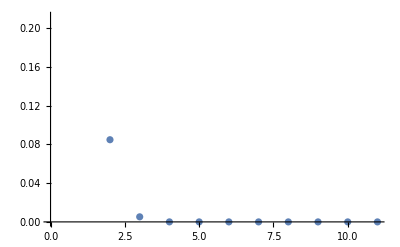

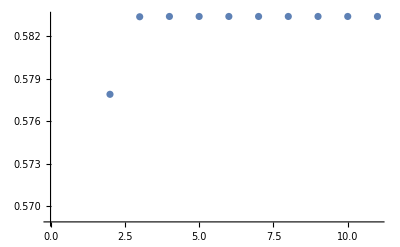

```mathematica
J0=1/3;
h0=1/2;
Js={J0};
hs={h0};
For[i=0,i<10,i++,Js=Append[Js,N[JR[Js[[-1]],hs[[-1]]]]];hs=Append[hs,N[hR[Js[[-1]],hs[[-1]]]]]]
ListPlot[Js]
ListPlot[hs]
```